This code is released under the GPL license. Copyright 2019 by Valerio Marra (valerio.marra@me.com)

### definitions

```mathematica
muln[Mp_,sigM_,S0_,S1_]:=(Log[10] (5 Mp S0-5 S1+(1+S0 sigM^2) Log[10]))/(25 S0);
sigln[sigM_,S0_]:=Log[10]/5 √(1/S0+sigM^2) ;
meanH[Mp_,sigM_,S0_,S1_]:=ⅇ^(muln[Mp,sigM,S0,S1]+sigln[sigM,S0]^2/2);
varH[Mp_,sigM_,S0_,S1_]:=ⅇ^(2 muln[Mp,sigM,S0,S1]+sigln[sigM,S0]^2) (-1+ⅇ^(sigln[sigM,S0]^2));
skew[Mp_,sigM_,S0_]:=√(-1+ⅇ^(sigln[sigM,S0]^2)) (2+ⅇ^(sigln[sigM,S0]^2));
```

### supernova data

```mathematica
(* Pantheon data from arXiv:1710.00845 *)
SetDirectory[NotebookDirectory[]];
Dimensions[datax=Import["data/low-sne.txt","Table","HeaderLines"->0]];
data=datax[[2;;]];
Row[{"{z_min,z_max}=",MinMax[data[[All,2]]]}]
TableForm[data[[;;5]],TableHeadings->{None, datax[[1]]}]

CovImp=Flatten[Import["data/cov_low-sne.dat","Table"]];
Nsn=CovImp[[1]];
Dimensions[covmu=Partition[CovImp[[2;;]],Nsn]];
covmu=covmu+DiagonalMatrix[data[[All,6]]^2];
inVcovmu=Inverse[covmu];
```

{z_min,z_max}={0.02348,0.14949}

#name | zcmb | zhel | dz | mb | dmb | x1 | dx1 | color | dcolor | 3rdvar | d3rdvar | cov_m_s | cov_m_c | cov_s_c | set | ra | dec
06D2fb | 0.12531 | 0.12531 | 0. | 19.4684 | 0.10355 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
744 | 0.12679 | 0.12679 | 0. | 19.5429 | 0.11965 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1241 | 0.08859 | 0.08859 | 0. | 18.6435 | 0.10605 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1371 | 0.11782 | 0.11782 | 0. | 19.1935 | 0.0991 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1794 | 0.14055 | 0.14055 | 0. | 19.871 | 0.11635 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0

### calibration prior determination

```mathematica
(* determination of H_0 from arXiv:1903.07603 *)
H0R19=74.03;
sigH0R19=1.42;
q0fid=-0.55;

ones=ConstantArray[1,Nsn];
Sum00=ones.inVcovmu.ones;
cc=299792458/1000;
mo[z_,H0_,q0_,M_]:=5 Log10[1+(1-q0)/2 z]+5Log10[cc z]+25+M-5Log10[H0];
ztab=data[[All,2]];
mutab=data[[All,5]];
vecmoi=mutab-mo[ztab,1,q0fid,0]; (* putting M-5Log10[H0] to zero *)
Sum10=vecmoi.inVcovmu.ones;
```

```mathematica
root=FindRoot[{meanH[Mp,sigM,Sum00,Sum10],varH[Mp,sigM,Sum00,Sum10]}=={H0R19,sigH0R19^2},{{Mp,-19},{sigM,0.04}}];
Row[{"Calibration prior on M_B: ",root}]

MpP=root[[1,2]];
sigMpP=root[[2,2]];
skew[MpP,sigMpP,Sum00];
```

Calibration prior on M_B: {Mp→-19.2245,sigM→0.0405094}

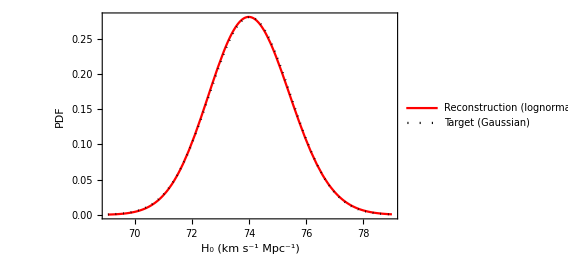

postH.pdf

```mathematica
po=Plot[{PDF[LogNormalDistribution[muln[MpP,sigMpP,Sum00,Sum10],sigln[sigMpP,Sum00]],h],PDF[NormalDistribution[H0R19,sigH0R19],h]},{h,H0R19-3.5sigH0R19,H0R19+3.5sigH0R19},Frame->True,PlotStyle->{{Thick,Red},{ Dotted,Black}},FrameStyle->16,FrameLabel->{"H_0 (km s^-1 Mpc^-1)","PDF"},PlotLegends->Placed[{"Reconstruction (lognormal)","Target (Gaussian)"},Above(*{Left,Top}*)],ImageSize->420]
Export["postH.pdf",po]
```